# II. Normal Distribution

## Författare

Stefan Josefsson, stejos@kth.se
Joe Huldén, joeda@kth.se

## Mattematiskt tillvägagångsätt

U1. Täthetsfunktionen för summan av tiden mellan n stycken samtal kan beskrivas av  pdf_n(s)=∫_(∀t) pdf_1(s-t)pdf_(n-1)(t)dt. Vi är intresserade av snittiden mellan samtalen vid n samtal varför vi får täthetsfunktionen pdf_n(s)=∫_(∀t) pdf_1((s-t) / k)pdf_(n-1)(t / k)dt, k=20. Integration över denna täthetsfunktionen ger oss fördelningsfunktionen för valt intervall. Denna beskriver då sannolikheten för att snittiden mellan två samtal understiger något värde.
Normalapproximation av täthetsfunktionen erhålles med hjälp av: 1/n∑_(i=1)^n 𝔵_i=𝔵̄(\[Distributed])^CLT N(μ,σ) Denna säger att snittiden mellan samtalen givet n stokastiska variabler kan skattas till en normalfördelning med  μ=1/n∑_(i=1)^n E[𝔵_i],σ^2=^(indep.)1/n^2∑_(i=1)^n V[𝔵_i]
Men väntevärdet är redan kännt och uppgår för alla stokastiska variabler till 3. Standardavvikelsen vidare beräknas genom V(X) = E[(X-my)^2]. Denna normalapproximation N(μ,σ) är den approximerade täthetsfunktionen. Integration över denna ger då fördelningsfunktionen. Både den exakta täthetsfunktion, fördelningsfunktion samt approximerade täthetsfunktion samt fördelningsfunktion krävs för beräkning av det absoluta och relativa felet. Det absoluta felet uppgår till absolutbeloppet av differensen mellan dessa funktioner. Det relativa felet är det absoluta felet genom den exakta täthetsfunktion resp fördelningsfunktion.

U2. Samtalen inträffar oberoende av varandra. Om flera samtal har inkommit under en tidsperiod påverkar det ej samtal som inträffar under en senare period. Detta medför att sannolikhetsfunktionen för antalet samtal under perioden en timma är poisson-fördelad. Då väntevärdet för tiden mellan samtal är 3 min. Kan vi definiera intensiteten, antalet samtal per tidsenhet till λ= 1/3samtal / min. Om tiden uppgår till 60 minuter får vi därför 60/3=20 samtal i genomsnitt. Detta medför att sannolikhetsfunktionen för antalet samtal under loppet av en timma kan beskrivas med X∈Po(60). Där X är antalet samtal. X∈Px(k)= μ^k/(k!)ℯ^-k. Med hjälp av mathematicas PoissonDistribution visas detta resultat. 
Poisson-fördelning kan approximeras med normalfördelning förutsatt tillräckligt stora μ. Vilket då lyder X∈ Ν(μ,√μ). Med hjälp av mathematicas Normaldistrubtion visas detta resultat. Det absoluta felet samt det relativa felet visas därefter genom jämförelse av dessa grafer.

## Diskussion

I uppgift 1. En förusättning för att approximationen skall vara användbar är att antalet stokastiska variabler ej är för litet. Desto större n desto större likhet med normalkurvan. I uppgift 1 kan det konstateras att approximationen i närheten av väntevärde är mer korrekt än i andra punkter. 

I uppgift 2. Som tidigare nämnts krävs ett tillräckligt stort μ för att approximationen skall ge ett acceptabelt resultat. För μ=20 är felet relativt litet. Det relativa felet är väldigt stort om man betraktar fler samtal än 30, men motsvarande absoluta fel håller sig ganska konstant.

## Grafer

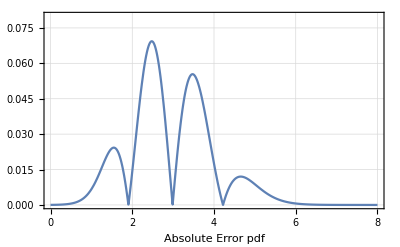
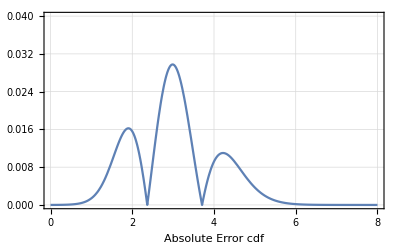
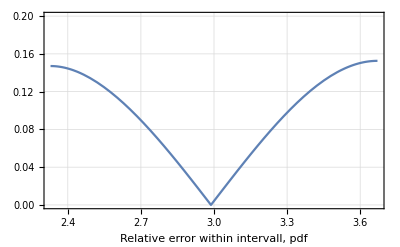
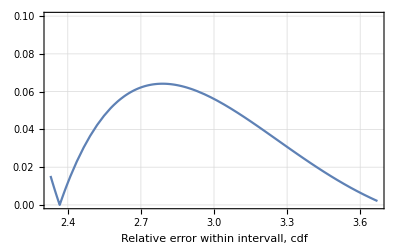
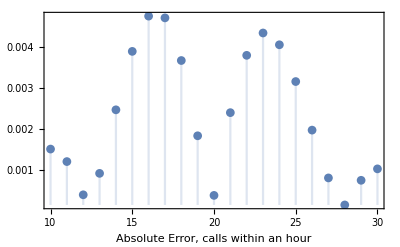
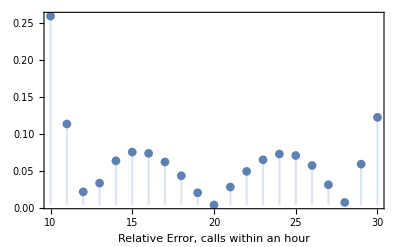

## Kod

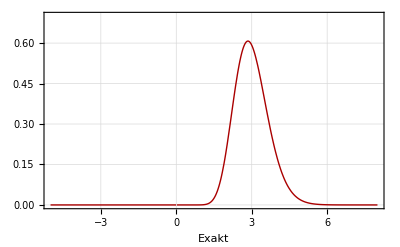

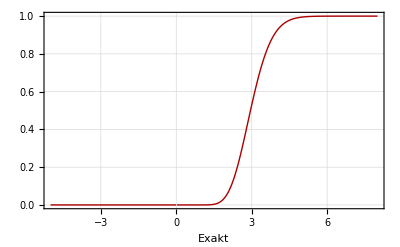

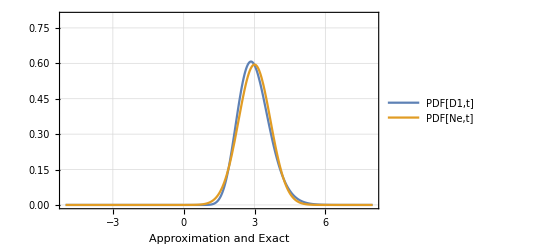

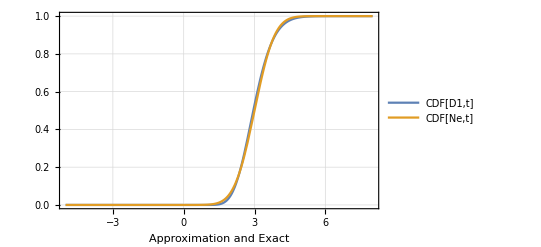

-Graphics-

-Graphics-

-Graphics-

-Graphics-

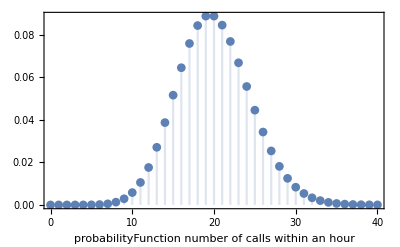

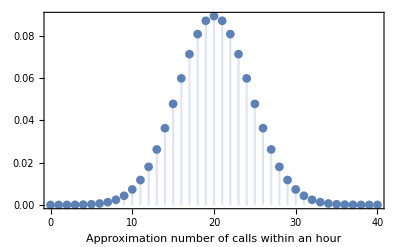

-Graphics-

-Graphics-

```mathematica
ClearAll["`*"]
σ = 3;

n = 20;
Subscript[λ, 1] = n/σ; (*testar detta nu*)
Subscript[λ, 2] = 1/σ;
D1 = ErlangDistribution[20,Subscript[λ, 1]];
μ = StandardDeviation[ErlangDistribution[1,Subscript[λ, 2]]];

(*exakt*)
p1=Plot[PDF[D1,t],{t,-5,8},AxesLabel->{HoldForm[t],HoldForm[Subscript[pdf, 1][t]]},PlotStyle->Directive[Darker[Red],Thick],PlotRange->{0,0.70},Frame->True,FrameLabel-> "Exakt",GridLines->Automatic]
p2=Plot[CDF[D1,t],{t,-5,8},AxesLabel->{HoldForm[t],HoldForm[Subscript[cdf, 1][t]]},PlotStyle->Directive[Darker[Red],Thick], PlotRange->{0,1},Frame->True,FrameLabel-> "Exakt",GridLines->Automatic]

(*approximation med exakt*)
Ne = NormalDistribution[μ, σ/√n];
Plot[{PDF[D1,t],PDF[Ne,t]},{t,-5,8},AxesLabel->{HoldForm[t],HoldForm[pdf[t]]}, PlotRange->{0,0.8}, Frame->True,FrameLabel-> "Approximation and Exact",GridLines->Automatic,PlotLegends->"Expressions"]
Plot[{CDF[D1,t],CDF[Ne,t]},{t,-5,8},AxesLabel->{HoldForm[t],HoldForm[cdf[t]]}, PlotRange->{0,1},Frame->True,FrameLabel-> "Approximation and Exact",GridLines->Automatic,PlotLegends->"Expressions"]

(*absoluta felet hela intervall*)
Plot[{Abs[PDF[D1,t]-PDF[Ne,t]]},{t,0,8},AxesLabel->{HoldForm[t],HoldForm[pdf[t]]}, PlotRange->{0,0.08},Frame->True,FrameLabel-> "Absolute Error pdf",GridLines->Automatic]
Plot[{Abs[CDF[D1,t]-CDF[Ne,t]]},{t,0,8},AxesLabel->{HoldForm[t],HoldForm[cdf[t]]}, PlotRange->{0,0.04},Frame->True,FrameLabel-> "Absolute Error cdf",GridLines->Automatic]

(*relativa felet, svnärt intervall*)
Plot[{(Abs[PDF[D1,t]-PDF[Ne,t]])/PDF[D1,t]},{t,μ - σ/√20,μ + σ/√20},AxesLabel->{HoldForm[t],HoldForm[pdf[t]]}, PlotRange->{0,0.20},Frame->True,FrameLabel-> "Relative error within intervall, pdf",GridLines->Automatic]
Plot[{(Abs[CDF[D1,t]-CDF[Ne,t]])/CDF[D1,t]},{t,μ - σ/√20,μ + σ/√20},AxesLabel->{HoldForm[t],HoldForm[cdf[t]]}, PlotRange->{0,0.10},Frame->True,FrameLabel-> "Relative error within intervall, cdf",GridLines->Automatic]

(*Task 2*)

my=60/3 ;
(*Korrekta*)
DiscretePlot[PDF[PoissonDistribution[my],k],{k,0,40},PlotRange->All,PlotMarkers->Automatic, Frame->True,FrameLabel-> "probabilityFunction number of calls within an hour"]
(*Normalapproximation*)
DiscretePlot[PDF[NormalDistribution[my, Sqrt[my]],k],{k,0,40},PlotRange->All,PlotMarkers->Automatic,  Frame->True,FrameLabel-> "Approximation number of calls within an hour"]
(*Absoluta felet*)
DiscretePlot[Abs[PDF[PoissonDistribution[my],k] - PDF[NormalDistribution[my, Sqrt[my]],k]],{k,10,30},PlotRange->All,PlotMarkers->Automatic, Frame->True,FrameLabel-> "Absolute Error, calls within an hour"]
DiscretePlot[Abs[PDF[PoissonDistribution[my],k] - PDF[NormalDistribution[my, Sqrt[my]],k]] /PDF[PoissonDistribution[my],k],{k,10,30},PlotRange->All,PlotMarkers->Automatic, Frame->True,FrameLabel-> "Relative Error, calls within an hour"]
```